```mathematica
ClearAll[c,G,MSun,rhoRadBBN];

c=29979245800;                   (*velocidad de la luz:cm/s*)
G=66743/10^12;                   (*constante gravitacional:cm^3/(g s^2)*)
MSun=198847*10^28;               (*masa solar:g*)

rhoRadBBN=7331305019814086*10^11;
(*densidad de energía de radiación en BBN:erg/cm^3*)
```

```mathematica
ti=37/50;                       (*coordenada temporal de BBN:0.74 s*)
ai=83/500000000000;             (*factor de escala en BBN:1.66*10^-10*)
Hti=67/100;                     (*parámetro de Hubble en BBN:0.67 s^-1*)
```

```mathematica
ρ0[ξ_]:= ξ*rhoRadBBN
```

```mathematica
Cxi[ξ_]:= (4π G)/(3c^2)*ρ0[ξ]
```

```mathematica
ClearAll[sol];
```

```mathematica
tMin=-5;
(* n = -3 luego 
(Y[t])^((n-1)/2) ----> Y^-2
*)
```

```mathematica
ClearAll[sol,tBounce]
```

```mathematica
sol[ξ_]:=sol[ξ]=Quiet@NDSolve[{Y'[t]==v[t],v'[t]==2*Cxi[ξ]*(Y[t])^(-2),Y[ti]==1,v[ti]==2*Hti,WhenEvent[v[t]==0,"StopIntegration"]},{Y,v},{t,-1,ti},WorkingPrecision->40,AccuracyGoal->20,PrecisionGoal->20,Method->"StiffnessSwitching",MaxSteps->Infinity];
```

```mathematica
tBounce[ξ_]:=tBounce[ξ]=(Y/. sol[ξ][[1]])["Domain"][[1,1]];
```

```mathematica
tB= tBounce[1/10]
```

-0.04746362038132198989511785642416990909902

```mathematica
Yfunc[ξ_,t_]:=Y[t]/. sol[ξ][[1]];
vFunc[ξ_,t_]:=v[t]/. sol[ξ][[1]];
```

```mathematica
apos[ξ_,t_]:=ai*Sqrt[Yfunc[ξ,Abs[t]+tBounce[ξ]]];
```

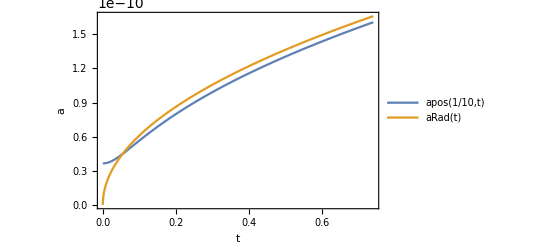

```mathematica
ar := ai/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
Plot[{apos[1/10, t],aRad[t]},{t,0,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0, PlotLegends->"Expressions"]
```

```mathematica
ρbh[ξ_,t_]:= ρ0[ξ]*(ai/apos[ξ, t])^4
```

```mathematica
ρbh[1/10,0]
```

3.1365644564325614773179805214246204445×10^28

```mathematica
ρbh[1/10, 10^(-4)]
```

3.136551618365132956578263780676870762×10^28

```mathematica
DotA[ξ_,t_]:=Sign[t]*(ai^2*vFunc[ξ,Abs[t]+tBounce[ξ]])/(2*apos[ξ,t]);
```

```mathematica
DotA[1/10, 0]
```

0

```mathematica
ρrad[ξ_, t_]:= (3c^2)/(8π G)(DotA[ξ, t]/apos[ξ, t])^2 -ρbh[ξ, t]
```

```mathematica
ρrad[1/10, 10^(-4)]
```

-3.1364861570292481610286195607281368508×10^28

```mathematica
ρrad[1/10, 0]
```

-3.1365644564325614773179805214246204445×10^28

```mathematica
HubbleParameter[ξ_, t_]:= √((8π G)/(3c^2)(ρrad[ξ, t]+ρbh[ξ, t]))
```

```mathematica
HubbleParameter[1/10, 0]
```

0.

```mathematica
HubbleParameter[1/10, 10^(-4)]
```

0.02018059158752194072247405612265839

```mathematica
5289.5069196841113186285097189208109531727050978632872936576626`36.94221135751255/5000
```

1.05790138393682226372570194378416219

```mathematica
MHubble[ξ_, t_]:= (4π c)/3*(ρrad[ξ, t]+ρbh[ξ, t])/(HubbleParameter[ξ, t])^3
```

```mathematica
γ := 0.2
Minic[ξ_, t_] := γ*MHubble[ξ, t]
```

```mathematica
Minic[1/10, 10^(-4)]
```

2.00043×10^39

```mathematica
Minic[1/10,10^(-4)]/MSun
```

1.00601×10^6

```mathematica
β = ρbh[1/10, 10^(-4)]/(ρrad[1/10, 10^(-4)]+ρbh[1/10, 10^(-4)])
```

47914.56782802453660952737819969629

```mathematica
xiCompareValues=10^-Range[10];
```

```mathematica
tForm=10^(-4);
```

```mathematica
tablaDatos=N[Table[{xi,HubbleParameter[xi,tForm],MHubble[xi,tForm],Minic[xi,tForm],Minic[xi,tForm]/MSun, ρbh[xi,tForm]/(ρrad[xi,tForm]+ρbh[xi,tForm])},{xi,xiCompareValues}],18];
```

```mathematica
Grid[Prepend[tablaDatos,{"ξ","H","\!\(\*SubscriptBox[\(M\), \(H\)]\)","\!\(\*SubscriptBox[\(M\), \(inic\)]\)","\!\(\*SubscriptBox[\(M\), \(inic\)]\)[MSun]", "β"}],Frame->All,Background->{None,{LightGray,None}},Alignment->Left]
```

ξ | H | M_H | M_inic | M_inic[MSun] | β
0.1 | 0.0201805915875219407 | 1.00021300298901301×10^40 | 2.00043×10^39 | 1.00601×10^6 | 47914.5678280245366
0.01 | 1.76430644245467153 | 1.14406939906465387×10^38 | 2.28814×10^37 | 11507. | 57.3311128485695644
0.001 | 168.962594717395522 | 1.19463660862992186×10^36 | 2.38927×10^35 | 120.156 | 0.05985810685739895
0.0001 | 4371.10869296716055 | 4.61779642915911806×10^34 | 9.23559×10^33 | 4.64457 | 0.00018292748002637793
0.00001 | 5251.64628661397315 | 3.84353572427370178×10^34 | 7.68707×10^33 | 3.86582 | 0.0000105905088019530146
1.×10^-6 | 5047.30553443256953 | 3.99914171554493949×10^34 | 7.99828×10^33 | 4.02233 | 1.01995929854800876×10^-6
1.×10^-7 | 5006.89579781598566 | 4.0314180540075966×10^34 | 8.06284×10^33 | 4.05479 | 1.01643364572466231×10^-7
1.×10^-8 | 5000.90715218033254 | 4.03624572494807784×10^34 | 8.07249×10^33 | 4.05965 | 1.01608732050781438×10^-8
1.×10^-9 | 5000.11252383456975 | 4.03688717356512775×10^34 | 8.07377×10^33 | 4.06029 | 1.01605273435944812×10^-9
1.×10^-10 | 5000.0134348709018 | 4.0369671755434591×10^34 | 8.07393×10^33 | 4.06038 | 1.01604927515639682×10^-10

```mathematica
formationHeaders = {"ξ", "H(t_form)","MHubble","Minic [g]", "Minic [Msun]", "β"};
```

```mathematica
csvPath=FileNameJoin[{NotebookDirectory[],"tabla_formacion_nm3.csv"}];
```

```mathematica
Export[csvPath,Prepend[tablaDatos,formationHeaders],"CSV"]
```

/home/iara/doctorado/tres incognitas/tabla_formacion_nm3.csv